```mathematica
With[
{B=1;A=1;Du=1;Dv=100},
f[x_, y_]:=A+x^2*y-(B+1)*x;
g[x_, y_] := -x^2*y+B*x;
a11[x_, y_] = Simplify[D[f[x,y],x]];
a12[x_, y_] = Simplify[D[f[x,y],y]];
a21[x_, y_] = Simplify[D[g[x,y],x]];
a22[x_, y_] = Simplify[D[g[x,y],y]];
x0 = A; y0 = B/A;
a110 = a11[x0, y0]; a120 = a12[x0, y0]; a210 = a21[x0, y0];a220 = a22[x0, y0];
(*KMD = {{a110 - k^2*Du-lambda, a120}, {a210, a220 - k^2*Dv - lambda}};
Quiet[solKMD = Solve[Det[KMD] ==0, lambda]];
Relambda11 = ComplexExpand[Re[lambda/.solKMD][[1]]]; Relambda21 = ComplexExpand[Re[lambda/.solKMD][[2]]]; Imlambda11 = ComplexExpand[Im[lambda/.solKMD][[1]]]/10; Imlambda21 = ComplexExpand[Im[lambda/.solKMD][[2]]]/10;
PicT = Plot[{Relambda11, Relambda21, Imlambda11,Imlambda21 }, {k, 0, 2}, PlotRange->{{0, 2}, {-2,2}}]*)
]
```

With::lvws: Variable B=1;A=1;Du=1;Dv=100 in local variable specification {B=1;A=1;Du=1;Dv=100} requires a value.

With[{B=1;A=1;Du=1;Dv=100},f[x_,y_]:=A+x^2 y-(B+1) x;g[x_,y_]:=-x^2 y+B x;a11[x_,y_]=Simplify[∂_x f[x,y]];a12[x_,y_]=Simplify[∂_y f[x,y]];a21[x_,y_]=Simplify[∂_x g[x,y]];a22[x_,y_]=Simplify[∂_y g[x,y]];x0=A;y0=B/A;a110=a11[x0,y0];a120=a12[x0,y0];a210=a21[x0,y0];a220=a22[x0,y0];KMD={{a110-k^2 Du-lambda,a120},{a210,a220-k^2 Dv-lambda}};Quiet[solKMD=Solve[Det[KMD]==0,lambda]];Relambda11=ComplexExpand[Re[lambda/.solKMD]⟦1⟧];Relambda21=ComplexExpand[Re[lambda/.solKMD]⟦2⟧];Imlambda11=1/10 ComplexExpand[Im[lambda/.solKMD]⟦1⟧];Imlambda21=1/10 ComplexExpand[Im[lambda/.solKMD]⟦2⟧];PicT=Plot[{Relambda11,Relambda21,Imlambda11,Imlambda21},{k,0,2},PlotRange→{{0,2},{-2,2}}]]

```mathematica
ClearAll@a
```

```mathematica
u0=Interpolation[Flatten[Table[{{x},a/.a->1+If[x==0||x==50,0,RandomReal[{-a/50,a/50}/.a->1]],{0}},{x,0,50}],1],InterpolationOrder->2];
v0=Interpolation[
Flatten[
Table[{{x},1+If[x==0||x==50,0,RandomReal[{-1/100,1/100}]],{0}},{x,0,50}]
,1]
,InterpolationOrder->2];
Show[Plot[u0[x],{x,0,50},PlotLegends->Automatic,ColorFunction->"SolarColors",FrameLabel->{"x"},ImageSize->Medium],Plot[v0[x],{x,0,50},ColorFunction->"Rainbow",FrameLabel->{"x"},ImageSize->Medium]]
```

InterpolatingFunction::dmval: Input value {0.00102143} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
noisefunc[const_,nperturb_: 10,noisefract_: 0.1]:=Module[{ipoints,ridx},ipoints=Table[{xi,const},{xi,0.0,1.0,0.01}];
ridx=Table[RandomInteger[{10,90}],{nperturb}];
Do[ipoints[[ridx[[ri]]]][[2]]+=noisefract*RandomReal[{-1,1}],{ri,nperturb}];
Return[Interpolation[ipoints,Method->"Spline"]]];
nfu = noisefunc[1.0];
nfv = noisefunc[1.0];
soluv=NDSolve[{D[u[x,t],t]==Du *Derivative[2,0][u][x,t]+a-(b+1) u[x,t]+v[x,t] (u[x,t])^2,D[v[x,t],t]==Dv *Derivative[2,0][v][x,t]+b u[x,t]-v[x,t] (u[x,t])^2,
u[x,0]==nfu[x],
v[x,0]==nfv[x],
Derivative[1,0][u][0,t]==0,
Derivative[1,0][u][L,t]==0,
Derivative[1,0][v][0,t]==0,
Derivative[1,0][v][L,t]==0}/.{L->50,Du->1,Dv->100,a->1,b->1},{u,v},{x,0,50},{t,0,0.05 4000},MaxSteps->{15,Infinity}]
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

{{u→InterpolatingFunction[…],v→InterpolatingFunction[…]}}

```mathematica
Plot3D[InterpolatingFunction[…][x,t],{x,0,50},{t,0,0.05 4000}]
```

-Graphics3D-

```mathematica
Export["C:/Users/Daria/Desktop/биофиз/brusselator/plots/",ListLinePlot[listTU]];
```

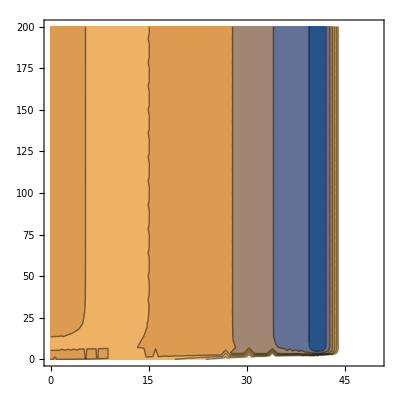

```mathematica
ContourPlot[InterpolatingFunction[…][x,t],{x,0,50},{t,0,0.05 4000}]
```

```mathematica
Plot3D[u[x,t],{x,0,50},{t,0,0.05 4000}]/.soluv⟦1⟧⟦1⟧⟦2⟧
```

ReplaceAll::reps: {InterpolatingFunction[{{0.,50.},{0.,200.}},{5,5,1,{15,235},{6,4},0,0,0,0,Automatic,{},{},False},{«1»},{Developer`PackedArrayForm,{0,3,6,9,12,«41»,138,141,144,147,«3476»},{1.,9.0072×10^15,0.000236341,1.,9.0072×10^15,0.000268898,1.,9.0072×10^15,0.000305481,1.00001,«31»,0.00388656,1.00047,9.0072×10^15,0.00446803,1.00059,9.0072×10^15,0.00503462,1.00072,9.0072×10^15,«10525»}},{Automatic,Automatic}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-Graphics3D-/.InterpolatingFunction[…]